```mathematica
Clear["Global`*"]
```

```mathematica
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))]
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]]
map3[x_,y_,μ_]=ComplexExpand[map[Re[map2[x,y,μ]],Im[map2[x,y,μ]],μ]]
```

x μ-x^2 μ+y^2 μ+ⅈ (y μ-2 x y μ)

x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3+ⅈ (y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3)

x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7+ⅈ (y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7)

```mathematica
imaginary = x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7;
real = y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;
```

```mathematica
mat = {{D[real,x],D[real,y]},{D[imaginary,x],D[imaginary,y]}};
mat2 ={{D[D[real,x],x],D[D[real,y],y]},{D[D[imaginary,x],x],D[D[imaginary,y],y]}};
```

```mathematica
autovj = Eigenvalues[mat];
autovh = Eigenvalues[mat2];
eigenvecj = Eigensystem[mat]/.μ-> 3.8;
eigenvech = Eigensystem[mat2];
autovetorj = Eigenvectors[mat];
FullSimplify[Dot[autovetorj⟦1,1⟧ ,autovetorj⟦2,1⟧]]
```

((-8 y^7 μ^4+12 y^5 μ^3 (1+(3+14 (-1+x) x) μ)-4 y^3 μ (1+μ+6 (1+5 (-1+x) x) μ^2+(1+10 (-1+x) x (2+7 (-1+x) x)) μ^3)+√(((1-2 x)^2+4 y^2) (1+4 μ ((-1+x) x-y^2+((-1+x)^2+y^2) (x^2+y^2) μ)) (1+4 μ^2 ((-1+x) x-y^2+((-1+x)^2 x^2+(-1-6 (-1+x) x) y^2+y^4) μ+((-1+x)^2+y^2) (x^2+y^2) μ^2+2 ((-1+x) x-y^2) ((-1+x)^2+y^2) (x^2+y^2) μ^3+((-1+x)^2+y^2)^2 (x^2+y^2)^2 μ^4)))+2 y (1+μ (1+μ+2 (-1+x) x (3+μ (3+μ (3+(-1+x) x (15+(3+14 (-1+x) x) μ)))))))/(-1+2 (x+(-1+2 x) ((-1+x) x-3 y^2) μ+(-1+2 x) ((-1+x) x-3 y^2) μ^2+3 (-1+2 x) ((-1+x)^2 x^2+(-1-10 (-1+x) x) y^2+5 y^4) μ^3+2 (-1+2 x) ((-1+x)^3 x^3-3 (-1+x) x (1+7 (-1+x) x) y^2+5 (1+7 (-1+x) x) y^4-7 y^6) μ^4))).(-((8 y^7 μ^4-12 y^5 μ^3 (1+(3+14 (-1+x) x) μ)+4 y^3 μ (1+μ+6 (1+5 (-1+x) x) μ^2+(1+10 (-1+x) x (2+7 (-1+x) x)) μ^3)+√(((1-2 x)^2+4 y^2) (1+4 μ ((-1+x) x-y^2+((-1+x)^2+y^2) (x^2+y^2) μ)) (1+4 μ^2 ((-1+x) x-y^2+((-1+x)^2 x^2+(-1-6 (-1+x) x) y^2+y^4) μ+((-1+x)^2+y^2) (x^2+y^2) μ^2+2 ((-1+x) x-y^2) ((-1+x)^2+y^2) (x^2+y^2) μ^3+((-1+x)^2+y^2)^2 (x^2+y^2)^2 μ^4)))-2 y (1+μ (1+μ+2 (-1+x) x (3+μ (3+μ (3+(-1+x) x (15+(3+14 (-1+x) x) μ)))))))/(-1+2 (x+(-1+2 x) ((-1+x) x-3 y^2) μ+(-1+2 x) ((-1+x) x-3 y^2) μ^2+3 (-1+2 x) ((-1+x)^2 x^2+(-1-10 (-1+x) x) y^2+5 y^4) μ^3+2 (-1+2 x) ((-1+x)^3 x^3-3 (-1+x) x (1+7 (-1+x) x) y^2+5 (1+7 (-1+x) x) y^4-7 y^6) μ^4))))

```mathematica
n=8;
L={};
For[i=38 300.,i≤ 384 30,i++,
μ=i/3000.;
For[j=1,j<10,j++,
x0=RandomReal[];
y0=RandomReal[] 10^-1;
tab1=FindRoot[{Re[map3[x,y,μ]]== x,Im[map3[x,y,μ]]== y},{{x,x0},{y,y0}}];
L=Append[L,{μ,1. 10^-n Round[tab1⟦1,2⟧10^n],1. 10^-n Round[tab1⟦2,2⟧10^n]}];
tab1=FindRoot[{Re[map3[x,y,μ]]== x,Im[map3[x,y,μ]]== y},{{x,x0},{y,-y0}}];
L=Append[L,{μ,1. 10^-n Round[tab1⟦1,2⟧10^n],1. 10^-n Round[tab1⟦2,2⟧10^n]}];
]
]
L = DeleteDuplicates[L];
Clear[μ]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPointPlot3D[L,ViewPoint->{0,0,Infinity}];
ListPointPlot3D[L]
```

-Graphics3D-

```mathematica
tab1=FindRoot[{Re[map3[x,y,3.80]]== x,Im[map3[x,y,3.80]]== y},{{x,0.7},{y,0.1}}];
tab1⟦2,2⟧;
Round[tab1⟦2,2⟧10^8] 10^-8;
```

```mathematica
Lnum = {}
For[i=1,i<Length[L],i++,
AppendTo[Lnum,{L⟦i⟧,i}];]
(*AppendTo[Lnum⟦i⟧,i]]*)
```

{}

```mathematica
Length[Lnum]
Length[L]
```

732

733

```mathematica
Lnum⟦720⟧
```

{{3.83933,0.169174,0.},720}

```mathematica
afterw = Select[L,#⟦1⟧>3.8284 &];
beforew= Select[L, #⟦1⟧<3.8284 &];
```

```mathematica
ListPointPlot3D[beforew];
```

```mathematica
pontos = L;
groupA = Select[pontos, #⟦2⟧<0.1 &];
groupBstep = Select[pontos, #⟦2⟧>0.1 &];
groupB = Select[groupBstep, #⟦2⟧<0.2 &];
groupCstep = Select[pontos, #⟦2⟧>0.4 &];
groupC= Select[groupCstep, #⟦2⟧<0.6 &];
groupDstep = Select[pontos, #⟦2⟧>0.6 &];
groupD = Select[groupDstep, #⟦2⟧<0.8 &];
groupE = Select[pontos, #⟦2⟧>0.8 &];
```

```mathematica
ListPointPlot3D[groupE]
```

-Graphics3D-

```mathematica
groupD
```

{{3.80033,0.736865,0.},{3.801,0.736911,0.},{3.80133,0.736934,0.},{3.80167,0.736957,0.},{3.802,0.736981,0.},{3.80233,0.737004,0.},{3.80267,0.737027,0.},{3.803,0.73705,0.},{3.80333,0.737073,0.},{3.80367,0.737096,0.},{3.804,0.737119,0.},{3.80433,0.737142,0.},{3.80467,0.737165,0.},{3.805,0.737188,0.},{3.80567,0.737234,0.},{3.806,0.737257,0.},{3.80633,0.73728,0.},{3.80667,0.737303,0.},{3.80767,0.737372,0.},{3.808,0.737395,0.},{3.80833,0.737418,0.},{3.80867,0.737441,0.},{3.809,0.737464,0.},{3.80933,0.737487,0.},{3.81,0.737533,0.},{3.81033,0.737556,0.},{3.81067,0.737579,0.},{3.811,0.737602,0.},{3.81133,0.737625,0.},{3.81167,0.737648,0.},{3.812,0.737671,0.},{3.81233,0.737693,0.},{3.81267,0.737716,0.},{3.813,0.737739,0.},{3.81333,0.737762,0.},{3.81367,0.737785,0.},{3.814,0.737808,0.},{3.81433,0.737831,0.},{3.81467,0.737854,0.},{3.815,0.737877,0.},{3.81567,0.737923,0.},{3.816,0.737945,0.},{3.81633,0.737968,0.},{3.81667,0.737991,0.},{3.817,0.738014,0.},{3.81733,0.738037,0.},{3.81767,0.73806,0.},{3.818,0.738083,0.},{3.81833,0.738106,0.},{3.81867,0.738128,0.},{3.819,0.738151,0.},{3.81933,0.738174,0.},{3.81967,0.738197,0.},{3.82,0.73822,0.},{3.82033,0.738243,0.},{3.821,0.738288,0.},{3.82167,0.738334,0.},{3.822,0.738357,0.},{3.82267,0.738403,0.},{3.823,0.738425,0.},{3.82333,0.738448,0.},{3.82367,0.738471,0.},{3.824,0.738494,0.},{3.82433,0.738517,0.},{3.82467,0.738539,0.},{3.825,0.738562,0.},{3.82533,0.738585,0.},{3.82567,0.738608,0.},{3.826,0.73863,0.},{3.82633,0.738653,0.},{3.82667,0.738676,0.},{3.82733,0.738721,0.},{3.82767,0.738744,0.},{3.82833,0.73879,0.},{3.82867,0.738812,0.},{3.829,0.738835,0.},{3.82933,0.738858,0.},{3.83,0.738903,0.},{3.83033,0.738926,0.},{3.83067,0.738949,0.},{3.831,0.738972,0.},{3.83133,0.738994,0.},{3.83167,0.739017,0.},{3.832,0.73904,0.},{3.83233,0.739062,0.},{3.83267,0.739085,0.},{3.833,0.739108,0.},{3.83333,0.73913,0.},{3.83367,0.739153,0.},{3.834,0.739176,0.},{3.835,0.739244,0.},{3.83533,0.739266,0.},{3.83567,0.739289,0.},{3.836,0.739312,0.},{3.83633,0.739334,0.},{3.837,0.73938,0.},{3.83733,0.739402,0.},{3.83767,0.739425,0.},{3.838,0.739448,0.},{3.83833,0.73947,0.},{3.83867,0.739493,0.},{3.83933,0.739538,0.},{3.83967,0.739561,0.}}

```mathematica
groups1 = {groupB, groupC, groupE};
groups2 = {groupA, groupD};

thelistp = {{},{},{}};
thelistf = {{},{},{}};
thelistf2 = {{},{}};
```

thelistf -->  lista contendo uma sublista para cada “grupo” contido na lista groups.  Para cada sublista haverão 8 termos:  {gp1xf, gp1yf, gp2xf, gp2yf, ... }, sendo cada termo uma função interpolada de μ com relação a x ou y de cada ramo de um grupo (B1, B2, B3, B4).

thelistp -> lista contendo uma sublista para cada “grupo” contido na lista groups.  Para cada sublista haverão 4 termos:  {gp1, gp2, gp3, gp4 }, sendo cada termo uma lista contendo {μ, x, y} referentes a cada ramo de um grupo  (B1, B2, B3, B4).

```mathematica
For[i=1,i≤ Length[groups1],i++,
before = Select[groups1⟦i⟧,#⟦1⟧≤ 3.8284 &];
after = Select[groups1⟦i⟧, #⟦1⟧>3.8284 &];
gp1 = Select[before, #⟦3⟧≥ 0 &];
gp3 = Select[before, #⟦3⟧<0 &];
gp2 = Select[after,#⟦2⟧≥ before⟦Length[before],2⟧ &];
gp4 = Select[after,#⟦2⟧<before⟦Length[before],2⟧ &];
(* step com drop adicionado*)
gp1x = DeleteDuplicates[Drop[gp1,0,{3}]];
gp1y = DeleteDuplicates[Drop[gp1,0,{2}]];
gp2x = DeleteDuplicates[Drop[gp2,0,{3}]];
gp2y = DeleteDuplicates[Drop[gp2,0,{2}]];
gp3x = DeleteDuplicates[Drop[gp3,0,{3}]];
gp3y =DeleteDuplicates[Drop[gp3,0,{2}]];
gp4x = DeleteDuplicates[Drop[gp4,0,{3}]];
gp4y =DeleteDuplicates[Drop[gp4,0,{2}]];
gp1xf = Interpolation[gp1x];
gp1yf = Interpolation[gp1y];
gp2xf = Interpolation[gp2x];
gp2yf = Interpolation[gp2y];
gp3xf = Interpolation[gp3x];
gp3yf = Interpolation[gp3y];
gp4xf = Interpolation[gp4x];
gp4yf = Interpolation[gp4y];
AppendTo[thelistp⟦i⟧,gp1] ;
AppendTo[thelistp⟦i⟧,gp2];
AppendTo[thelistp⟦i⟧,gp3];
AppendTo[thelistp⟦i⟧,gp4];
AppendTo[thelistf⟦i⟧,gp1xf];
AppendTo[thelistf⟦i⟧,gp1yf];
AppendTo[thelistf⟦i⟧,gp2xf];
AppendTo[thelistf⟦i⟧,gp2yf];
AppendTo[thelistf⟦i⟧,gp3xf];
AppendTo[thelistf⟦i⟧,gp3yf];
AppendTo[thelistf⟦i⟧,gp4xf];
AppendTo[thelistf⟦i⟧,gp4yf];]
```

thelistf2 -->  lista contendo uma sublista para cada “grupo” contido na lista groups2.  Para cada sublista haverão 4 termos:  {gp1xf, gp1yf, gp2xf, gp2yf}, sendo cada termo uma função interpolada de μ com relação a x ou y de cada ramo de um grupo (A1, A2).

```mathematica
For[i=1,i≤ Length[groups2],i++,
gpp1 = Select[groups2⟦i⟧,#⟦1⟧≤ 3.8284 &];
gpp2 = Select[groups2⟦i⟧, #⟦1⟧>3.8284 &];
gpp1x = DeleteDuplicates[Drop[gpp1,0,{3}]];
gpp1y = DeleteDuplicates[Drop[gpp1,0,{2}]];
gpp2x = DeleteDuplicates[Drop[gpp2,0,{3}]];
gpp2y = DeleteDuplicates[Drop[gpp2,0,{2}]];
gpp1xf = Interpolation[gpp1x];
gpp1yf = Interpolation[gpp1y];
gpp2xf = Interpolation[gpp2x];
gpp2yf = Interpolation[gpp2y];
AppendTo[thelistf2⟦i⟧,gpp1xf];
AppendTo[thelistf2⟦i⟧,gpp1yf];
AppendTo[thelistf2⟦i⟧,gpp2xf];
AppendTo[thelistf2⟦i⟧,gpp2yf];]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

```mathematica
thelistf2⟦2⟧
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

autovjlist -->  lista contendo uma sublista para cada “grupo” contido na lista groups.  Para cada sublista haverá 4 termos:  {autovj1, autovj2, ...}, sendo cada termo uma função interpolada de μ com relação a seu autovalor de cada ramo de um grupo (B1, B2, B3, B4) da matriz jacobiana.

autovhlist -->  lista contendo uma sublista para cada “grupo” contido na lista groups.  Para cada sublista haverá 4 termos:  {autovh1, autovh2, ...}, sendo cada termo uma função interpolada de μ com relação a seu autovalor de cada ramo de um grupo (B1, B2, B3, B4) da matriz hessiana.

```mathematica
Clear[autovjlist]
```

```mathematica
autovjlist = {};
autovhlist = {};
For[i=1,i≤ Length[groups1],i++,
autovj1 [μ_]:= autovj/.{x-> thelistf⟦i,1⟧[μ],y-> thelistf⟦i,2⟧[μ]};
autovj2 [μ_]:= autovj/.{x-> thelistf⟦i,3⟧[μ],y-> thelistf⟦i,4⟧[μ]};
autovj3 [μ_]:= autovj/.{x-> thelistf⟦i,5⟧[μ],y-> thelistf⟦i,6⟧[μ]};
autovj4 [μ_]:= autovj/.{x-> thelistf⟦i,7⟧[μ],y-> thelistf⟦i,8⟧[μ]};
autovjgroup = {autovj1[μ], autovj2[μ], autovj3[μ], autovj4[μ]};
AppendTo[autovjlist, autovjgroup];
autovh1 [μ_]:= autovh/.{x-> thelistf⟦i,1⟧[μ],y-> thelistf⟦i,2⟧[μ]};
autovh2 [μ_]:= autovh/.{x-> thelistf⟦i,3⟧[μ],y-> thelistf⟦i,4⟧[μ]};
autovh3 [μ_]:= autovh/.{x-> thelistf⟦i,5⟧[μ],y-> thelistf⟦i,6⟧[μ]};
autovh4 [μ_]:= autovh/.{x-> thelistf⟦i,7⟧[μ],y-> thelistf⟦i,8⟧[μ]};
autovhgroup = {autovh1[μ], autovh2[μ], autovh3[μ], autovh4[μ]};
AppendTo[autovhlist, autovhgroup]]
```

```mathematica
autovjlist2 = {};
autovhlist2 = {};
For[i=1,i≤ Length[groups2],i++,
autovj1 [μ_]:= autovj/.{x-> thelistf2⟦i,1⟧[μ],y-> thelistf2⟦i,2⟧[μ]};
autovj2 [μ_]:= autovj/.{x-> thelistf2⟦i,3⟧[μ],y-> thelistf2⟦i,4⟧[μ]};
autovjgroup = {autovj1[μ], autovj2[μ]};
AppendTo[autovjlist2, autovjgroup];
autovh1 [μ_]:= autovh/.{x-> thelistf2⟦i,1⟧[μ],y-> thelistf2⟦i,2⟧[μ]};
autovh2 [μ_]:= autovh/.{x-> thelistf2⟦i,3⟧[μ],y-> thelistf2⟦i,4⟧[μ]};
autovhgroup = {autovh1[μ], autovh2[μ]};
AppendTo[autovhlist2, autovhgroup]]
```

```mathematica
autovjlist⟦1,1⟧;
```

```mathematica
Table[autovjlist⟦1,1,1,3,1,i,3,1,0,1,1⟧,{i,3,30}]
```

{{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833},{3.8,3.82833}}

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

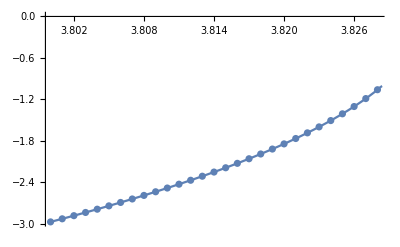

```mathematica
Show[ListPlot[Table[{i,autovjlist⟦1,1,1⟧/. μ-> i},{i,3.80,3.8284,0.001}]],Plot[autovjlist⟦1,1,1⟧,{μ,3.8,3.8284}]]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

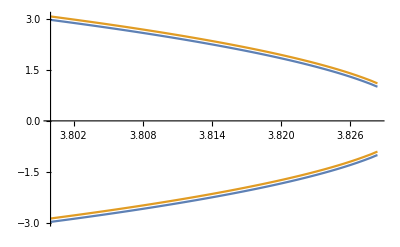

```mathematica
Plot[{autovjlist⟦1,1⟧,0.1+autovjlist⟦1,3⟧},{μ,3.8,3.8284}]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

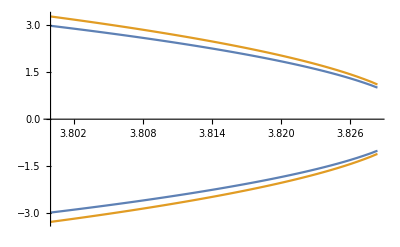

```mathematica
Plot[{autovjlist⟦2,1⟧,1.1autovjlist⟦2,3⟧},{μ,3.8,3.8284}]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

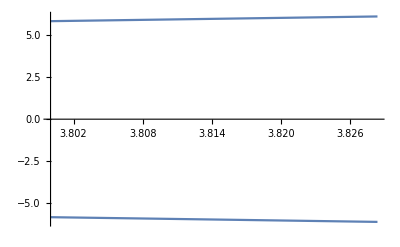

```mathematica
Plot[{autovjlist⟦3,1⟧,1.1autovjlist⟦3,3⟧},{μ,3.8,3.8284}]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

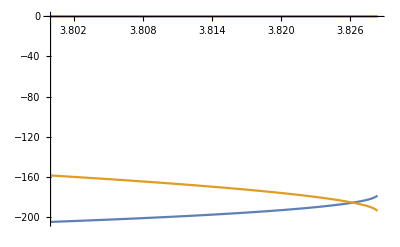

```mathematica
Plot[{autovhlist⟦1,1⟧,1.1autovhlist⟦1,3⟧},{μ,3.8,3.8284}]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

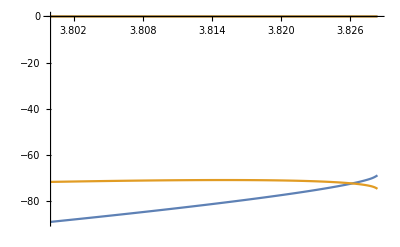

```mathematica
Plot[{autovhlist⟦2,1⟧,1.1autovhlist⟦2,3⟧},{μ,3.8,3.8284}]
```

Abaixo, comportamento que indica que o grupo E possui pouca contribuição (...), porque o inverso da frequência (...) ----> buscar entender melhor <-----

```mathematica
autovhlist/. μ-> 3.8
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{{0,-205.304},{0,4.40907×10^12},{0,-144.452},{0,3.1709×10^11}},{{0,-88.9325},{0,2.49561×10^12},{0,-65.1106},{0,2.47144×10^13}},{{0,484.658},{0,89.4655},{0,692.148},{0,1.164×10^7}}}

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

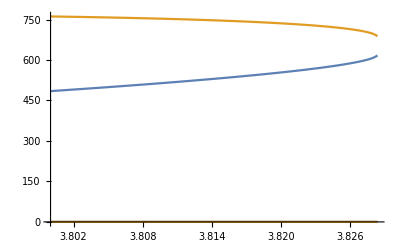

```mathematica
Plot[{autovhlist⟦3,1⟧,1.1autovhlist⟦3,3⟧},{μ,3.8,3.8284}]
```

Código com a mesma funcionalidade de autovjlist para testar o funcionamento de forma separada de cada elemento que estaria contido na lista.
Em seguida, um plot dos autovalores em função de μ para os 4 autovj’s.

```mathematica
autovj1 [μ_]= autovj/.{x-> thelistf⟦1,1⟧[μ],y-> thelistf⟦1,2⟧[μ]};
autovj2 [μ_]= autovj/.{x-> thelistf⟦1,3⟧[μ],y-> thelistf⟦1,4⟧[μ]};
autovj4 [μ_]= autovj/.{x-> thelistf⟦1,7⟧[μ],y-> thelistf⟦1,8⟧[μ]};
autovj3 [μ_]= autovj/.{x-> thelistf⟦1,5⟧[μ],y-> thelistf⟦1,6⟧[μ]};
```

```mathematica
autovj1[3.81]
```

{-2.48187,2.48187}

InterpolatingFunction::dmval: Input value {3.8284} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

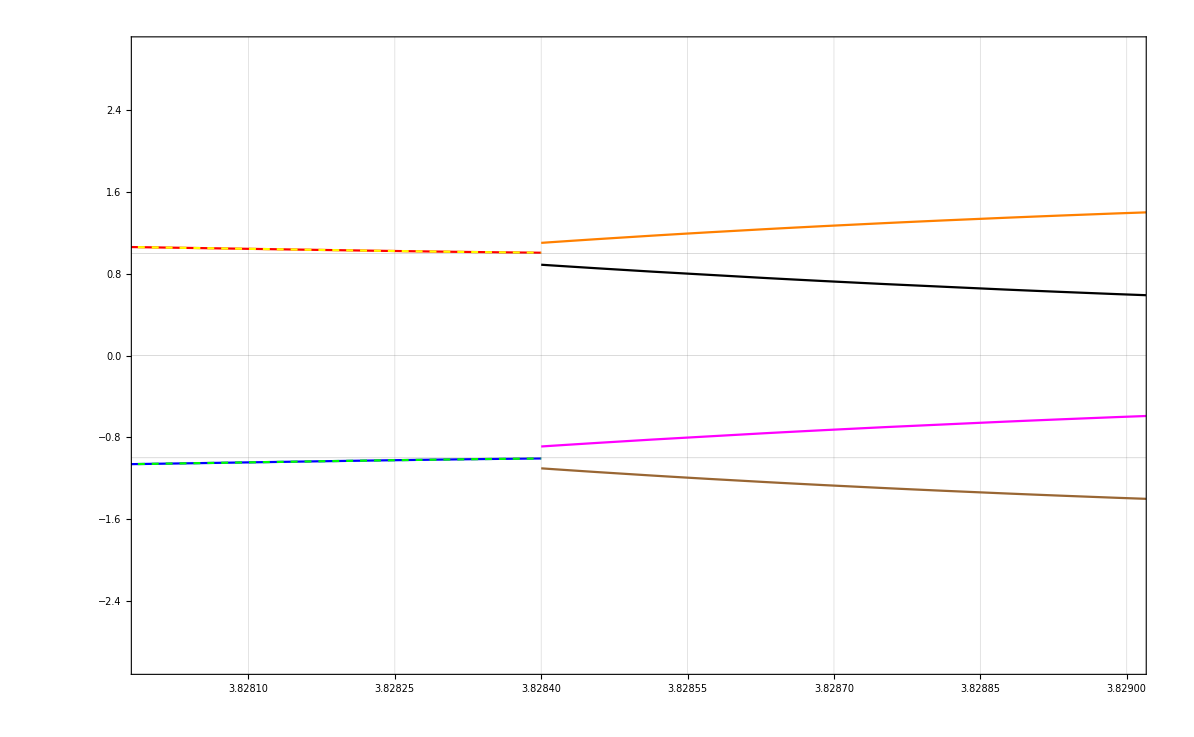

```mathematica
Show[
Plot[autovj1[μ]⟦1⟧,{μ,3.82,3.8284},PlotRange->{{3.828,3.829},{-3,3}},PlotStyle->Blue,Frame->True,GridLines->{Automatic, {-1,0,1}}],Plot[autovj1[μ]⟦2⟧,{μ,3.82,3.8284},PlotRange->{-2,2},PlotStyle->Red],
Plot[autovj2[μ]⟦1⟧,{μ,3.8284,3.84},PlotRange->{-2,2},PlotStyle->Brown],
Plot[autovj2[μ]⟦2⟧,{μ,3.8284,3.84},PlotRange->{-2,2},PlotStyle->Orange],
Plot[autovj3[μ]⟦1⟧,{μ,3.82,3.8284},PlotRange->{-2,2},PlotStyle->{Green,Dashed}],
Plot[autovj3[μ]⟦2⟧,{μ,3.82,3.8284},PlotRange->{-2,2},PlotStyle->{Yellow,Dashed}],
Plot[autovj4[μ]⟦1⟧,{μ,3.8284,3.84},PlotRange->{-2,2},PlotStyle->Magenta],
Plot[autovj4[μ]⟦2⟧,{μ,3.8284,3.84},PlotRange->{-2,2},PlotStyle->Black]
]
```

Tentativas de calcular uma média ponderada dos autovalores da Hessiana.

```mathematica
xyz[μ_]= (thelistf⟦1,1⟧[μ])/Abs[autovhlist⟦1,1,2⟧]+(thelistf⟦1,5⟧[μ])/Abs[autovhlist⟦1,3,2⟧]+(thelistf⟦2,1⟧[μ])/Abs[autovhlist⟦2,1,2⟧]+(thelistf⟦2,5⟧[μ])/Abs[autovhlist⟦2,3,2⟧]+(thelistf⟦3,1⟧[μ])/Abs[autovhlist⟦3,1,2⟧]+(thelistf⟦3,5⟧[μ])/Abs[autovhlist⟦3,3,2⟧]+(thelistf2⟦1,1⟧[μ])/Abs[autovhlist2⟦1,1,2⟧]+(thelistf2⟦2,1⟧[μ])/Abs[autovhlist2⟦2,1,2⟧];
```

```mathematica
Abs[autovhlist2⟦2,1,1⟧]/.μ-> 3.82
```

0

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

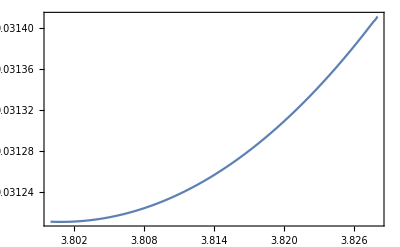

```mathematica
Plot[xyz[μ],{μ,3.8,3.828},Frame->True]
```

```mathematica
media[μ_]= thelistf⟦1,1⟧[μ]+thelistf⟦1,3⟧[μ]+thelistf⟦2,1⟧[μ]+thelistf⟦2,3⟧[μ]+thelistf⟦3,1⟧[μ]+thelistf⟦3,3⟧[μ]+thelistf2⟦1,1⟧[μ]+thelistf2⟦2,1⟧[μ];
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

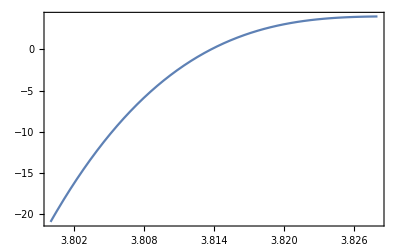

```mathematica
Plot[media[μ],{μ,3.8,3.828},Frame->True]
```

InterpolatingFunction[…]

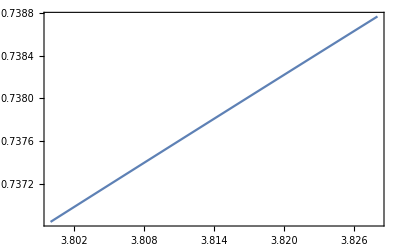

```mathematica
thelistf2⟦2,1⟧
Plot[thelistf2⟦2,1⟧[μ],{μ,3.8,3.828},Frame->True]
```

```mathematica
x = 0.1;
listpoints = {};
For[μ = 3.8, μ<3.835,μ=μ+0.0001,
(*For[i=1,i<100,i++,
x = μ x(1-x)
];*)
AppendTo[listpoints,{μ,x}];
For[i=1,i<100,i++,
x =μ x(1-x);
AppendTo[listpoints,{μ,x}];
]
]
```

```mathematica
x = 0.5;
listpointsx = {};
μ = 3.8;
AppendTo[listpointsx,x];
For[i=1,i<100,i++,
x =μ x(1-x);
AppendTo[listpointsx,x];
]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

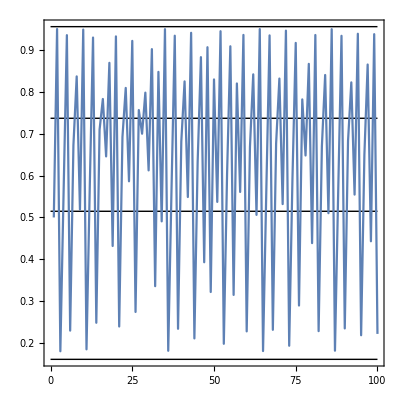

```mathematica
Show[Graphics[Line[{{0,thelistf⟦1,1⟧[3.8]},{100,thelistf⟦1,1⟧[3.8]}}]],
Graphics[Line[{{0,thelistf⟦2,1⟧[3.8]},{100,thelistf⟦2,1⟧[3.8]}}]],
Graphics[Line[{{0,thelistf⟦3,1⟧[3.8]},{100,thelistf⟦3,1⟧[3.8]}}]],
Graphics[Line[{{0,thelistf2⟦2,1⟧[3.8]},{100,thelistf2⟦2,1⟧[3.8]}}]],
ListPlot[listpointsx,PlotStyle->PointSize[0.005],Frame->True, Joined-> True],PlotRange-> All,Frame-> True,  AspectRatio-> 1]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.8284} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

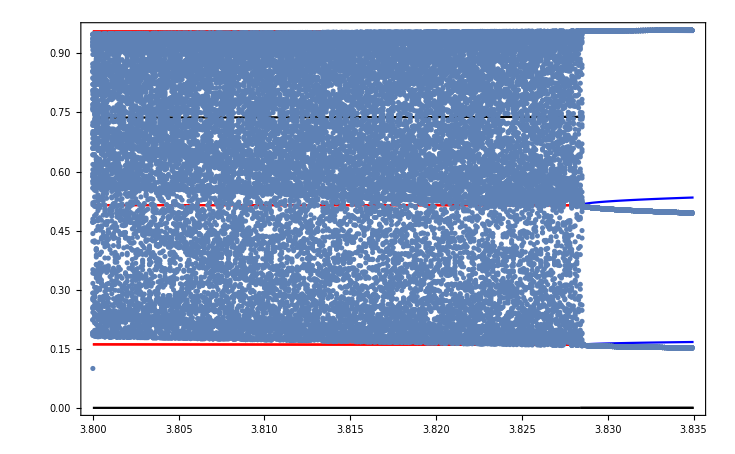

```mathematica
Show[Plot[{thelistf⟦1,1⟧[μ],thelistf⟦1,5⟧[μ],thelistf⟦2,1⟧[μ],thelistf⟦2,5⟧[μ],thelistf⟦3,1⟧[μ],thelistf⟦3,5⟧[μ]},{μ,3.8,3.8284},PlotStyle->Red],
Plot[{thelistf2⟦1,1⟧[μ],thelistf2⟦2,1⟧[μ]},{μ,3.8,3.8284},PlotStyle->Black],
Plot[{thelistf⟦1,3⟧[μ],thelistf⟦1,7⟧[μ],thelistf⟦2,3⟧[μ],thelistf⟦2,7⟧[μ],thelistf⟦3,3⟧[μ],thelistf⟦3,7⟧[μ]},{μ,3.8284,3.835},PlotStyle->Blue],
Plot[{thelistf2⟦1,2⟧[μ],thelistf2⟦2,2⟧[μ]},{μ,3.8284, 3.835},PlotStyle->Black],
ListPlot[listpoints,PlotStyle->PointSize[0.005],Frame->True],PlotRange-> All,Frame-> True]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.8284} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

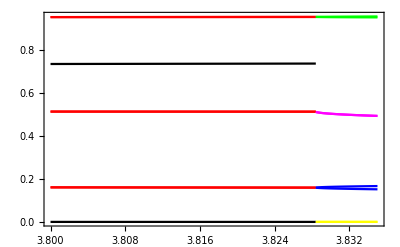

```mathematica
Show[Plot[{thelistf⟦1,1⟧[μ],thelistf⟦1,5⟧[μ],thelistf⟦2,1⟧[μ],thelistf⟦2,5⟧[μ],thelistf⟦3,1⟧[μ],thelistf⟦3,5⟧[μ]},{μ,3.8,3.8284},PlotStyle->Red],
Plot[{thelistf2⟦1,1⟧[μ],thelistf2⟦2,1⟧[μ]},{μ,3.8,3.8284},PlotStyle->Black],
Plot[{thelistf⟦1,3⟧[μ],thelistf⟦1,7⟧[μ]},{μ,3.8284,3.835},PlotStyle->Blue],
Plot[{thelistf⟦2,7⟧[μ],thelistf⟦2,7⟧[μ]},{μ,3.8284,3.835},PlotStyle->Magenta],
Plot[{thelistf⟦3,3⟧[μ],thelistf⟦3,7⟧[μ]},{μ,3.8284,3.835},PlotStyle->Green],
Plot[{thelistf2⟦1,2⟧[μ],thelistf2⟦2,2⟧[μ]},{μ,3.8284, 3.835},PlotStyle->Yellow],
PlotRange-> All,Frame-> True]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Part::partd: Part specification Plot[autovjlist]⟦1,1,1⟧ is longer than depth of object.

InterpolatingFunction::dmval: Input value {3.82} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

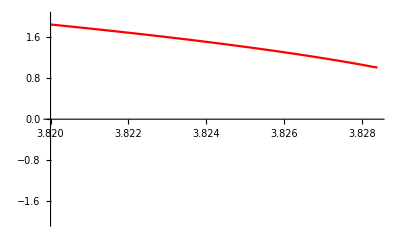
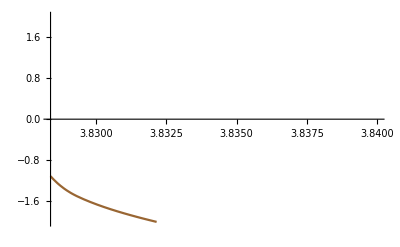
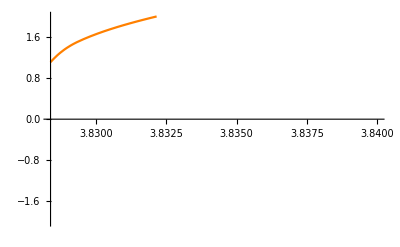
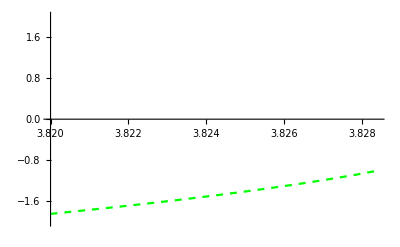
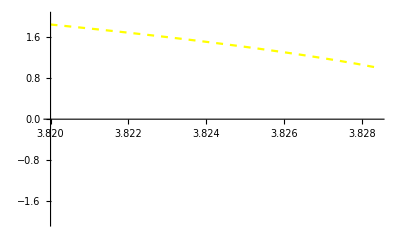
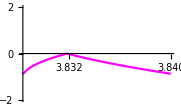
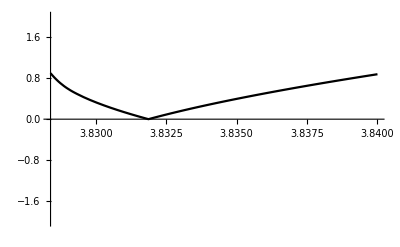
Show[Plot[autovjlist]⟦1,1,1⟧,{μ,3.82,3.8284},PlotRange→{{3.828,3.829},{-3,3}},PlotStyle→RGBColor[0, 0, 1],Frame→True,GridLines→{Automatic,{-1,0,1}},-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-]

```mathematica
Show[Plot[autovjlist]⟦1,1,1⟧,{μ,3.82,3.8284},PlotRange->{{3.828,3.829},{-3,3}},PlotStyle->Blue,Frame->True,GridLines->{Automatic, {-1,0,1}},Plot[autovjlist⟦1,1,2⟧,{μ,3.82,3.8284},PlotRange->{-2,2},PlotStyle->Red],
Plot[autovjlist⟦1,2,1⟧,{μ,3.8284,3.84},PlotRange->{-2,2},PlotStyle->Brown],
Plot[autovjlist⟦1,2,2⟧,{μ,3.8284,3.84},PlotRange->{-2,2},PlotStyle->Orange],
Plot[autovjlist⟦1,3,1⟧,{μ,3.82,3.8284},PlotRange->{-2,2},PlotStyle->{Green,Dashed}],
Plot[autovjlist⟦1,3,2⟧,{μ,3.82,3.8284},PlotRange->{-2,2},PlotStyle->{Yellow,Dashed}],
Plot[autovjlist⟦1,4,1⟧,{μ,3.8284,3.84},PlotRange->{-2,2},PlotStyle->Magenta],
Plot[autovjlist⟦1,4,2⟧,{μ,3.8284,3.84},PlotRange->{-2,2},PlotStyle->Black]]
```

InterpolatingFunction::dmval: Input value {3.82} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

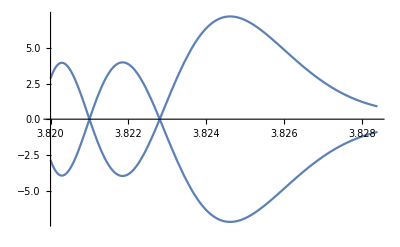

```mathematica
Plot[autovjlist⟦1,4⟧,{μ,3.82,3.8284}]
```

```mathematica
autovjlist⟦1,1⟧
```

InterpolatingFunction::dmval: Input value {3.835} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-1891.31,1891.31}

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

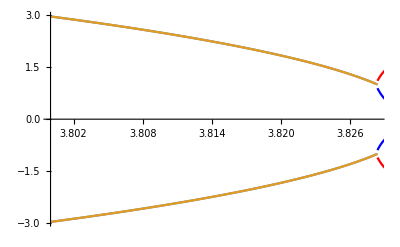

```mathematica
Show[
Plot[{autovjlist⟦1,1⟧,autovjlist⟦1,3⟧},{μ,3.8,3.8284}],
Plot[autovjlist⟦1,2⟧,{μ,3.8284,3.835},PlotStyle->Red],
Plot[autovjlist⟦1,4⟧,{μ,3.8284,3.835}, PlotStyle->Blue]]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

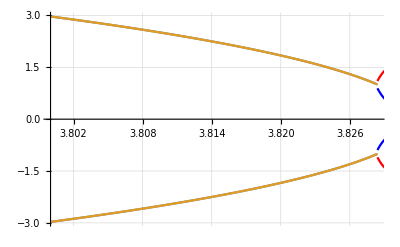

```mathematica
Show[
Plot[{autovjlist⟦2,1⟧,autovjlist⟦2,3⟧},{μ,3.8,3.8284}],
Plot[autovjlist⟦2,2⟧,{μ,3.8284,3.835},PlotStyle->Red],
Plot[autovjlist⟦2,4⟧,{μ,3.8284,3.835}, PlotStyle->Blue], GridLines-> Automatic]
```

InterpolatingFunction::dmval: Input value {3.825} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

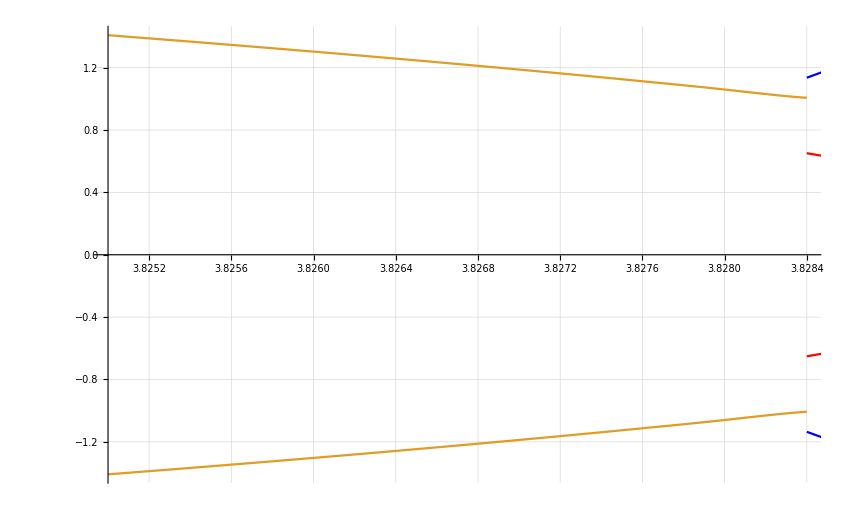

```mathematica
Show[
Plot[{autovjlist⟦3,1⟧,autovjlist⟦2,3⟧},{μ,3.825,3.8284}],
Plot[autovjlist⟦3,2⟧,{μ,3.8284,3.835},PlotStyle->Red],
Plot[autovjlist⟦3,4⟧,{μ,3.8284,3.835}, PlotStyle->Blue], GridLines-> Automatic]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

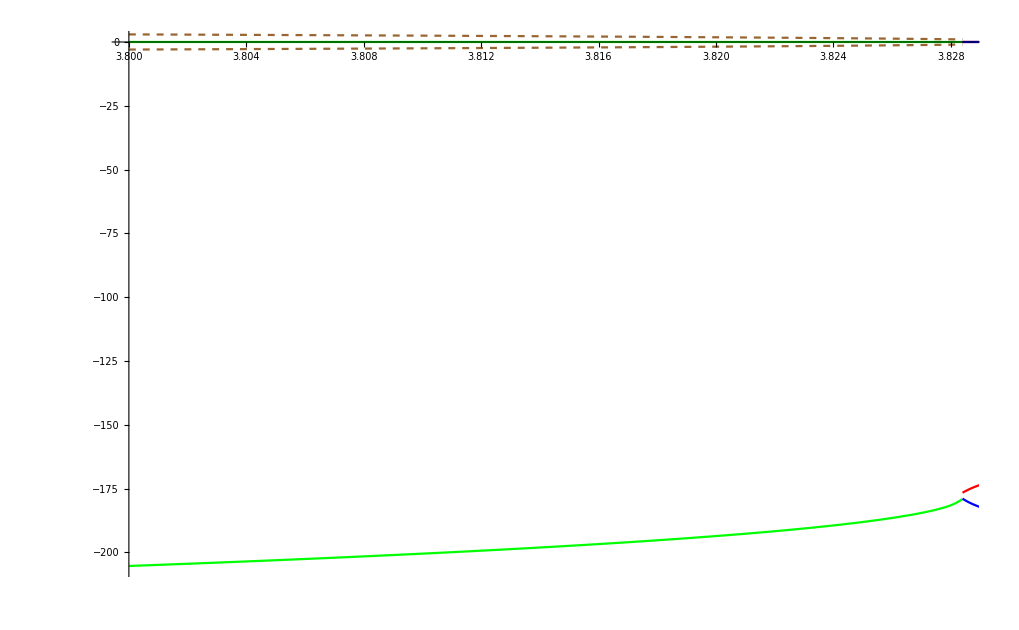

```mathematica
Show[
Plot[autovhlist⟦1,1⟧,{μ,3.8,3.8284}, PlotStyle->Green],
Plot[autovjlist⟦2,3⟧,{μ,3.8,3.8284}, PlotStyle->{Brown, Dashed}],
Plot[autovhlist⟦1,2⟧,{μ,3.8284,3.84},PlotStyle->Red],
Plot[autovhlist⟦1,4⟧,{μ,3.8284,3.84}, PlotStyle->Blue]]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

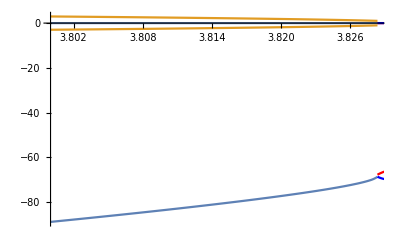

```mathematica
Show[
Plot[{autovhlist⟦2,1⟧,autovjlist⟦2,3⟧},{μ,3.8,3.8284}],
Plot[autovhlist⟦2,2⟧,{μ,3.8284,3.84},PlotStyle->Red],
Plot[autovhlist⟦2,4⟧,{μ,3.8284,3.84}, PlotStyle->Blue]]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

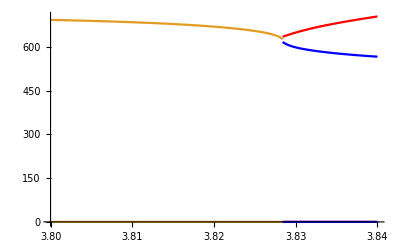

```mathematica
Show[
Plot[{autovhlist⟦3,1⟧,autovhlist⟦3,3⟧},{μ,3.8,3.8284}],
Plot[autovhlist⟦3,2⟧,{μ,3.8284,3.84},PlotStyle->Red],
Plot[autovhlist⟦3,4⟧,{μ,3.8284,3.84}, PlotStyle->Blue], PlotRange-> All]
```

InterpolatingFunction::dmval: Input value {3.8284} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

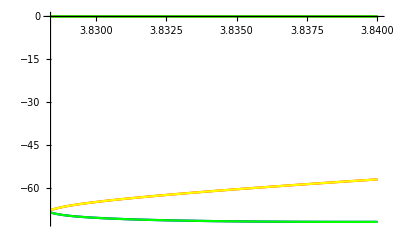

```mathematica
Show[
Plot[autovhlist⟦2,2⟧,{μ,3.8284,3.84},PlotStyle->Red],
Plot[autovhlist⟦2,4⟧,{μ,3.8284,3.84}, PlotStyle->Blue],
Plot[autovhlist⟦2,2⟧,{μ,3.8284,3.84},PlotStyle->Yellow],
Plot[autovhlist⟦2,4⟧,{μ,3.8284,3.84}, PlotStyle->Green], PlotRange-> All]
```

InterpolatingFunction::dmval: Input value {3.8284} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

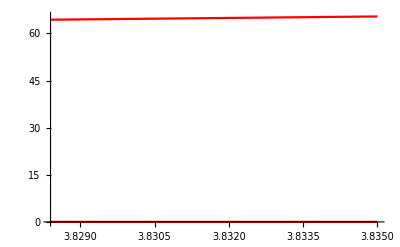

```mathematica
Plot[autovhlist2⟦2,2⟧,{μ,3.8284,3.835},PlotStyle->Red]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

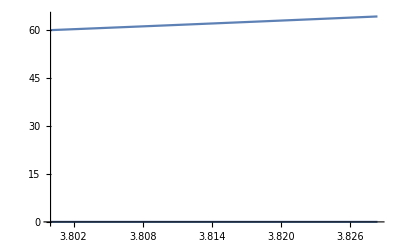

```mathematica
Plot[autovhlist2⟦2,1⟧,{μ,3.8,3.8284}]
```

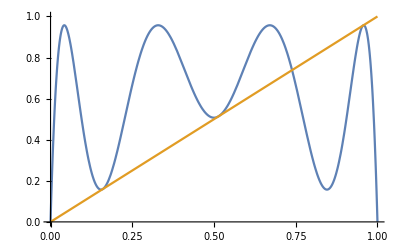

```mathematica
Plot[{map3[x,0,3.8284],x},{x,0,1}]
```

```mathematica
Manipulate[Plot[{map3[x,0,μ],x},{x,0,1}],{μ,2,4}]
```

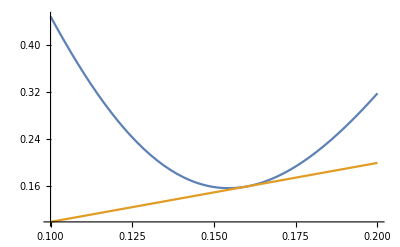

```mathematica
Plot[{map3[x,0,3.8284],x},{x,0.1,0.2}]
```

```mathematica
Plot3D[{x,Re[map3[x,y,3.8285]]},{x,0,1},{y,-0.07,0.07},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[{x,Re[map3[x,y,3.8284]]},{x,0.15,0.18},{y,-0.04,0.04}]
```

-Graphics3D-

```mathematica
Manipulate[Plot3D[{x,Re[map3[x,y,μ]]},{x,0.4,0.6},{y,-0.04,0.04},PlotRange->{0.4,0.6}],{μ,3.8,3.9,0.0001}]
```

```mathematica
Manipulate[Plot3D[{x,Re[map3[x,y,μ]]},{x,0.9,1.05},{y,-0.04,0.04},PlotRange->{0.9,1.05}],{μ,3.8,3.9,0.0001}]
```

```mathematica
Manipulate[Plot3D[{x,Re[map3[x,y,μ]]},{x,0.1,0.2},{y,-0.04,0.04},PlotRange->{0.1,0.3}],{μ,3.8,3.8285,0.0001}]
```

```mathematica
Plot3D[{Im[map3[x,y,3.8]],y},{x,0,1},{y,-0.04,0.04},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot[thelistf⟦1,2⟧[μ],{μ,3.8,3.8284}]
```

```mathematica
ClearAll[CobwebPlot]
Options[CobwebPlot]=Join[{CobStyle->Automatic},Options[Graphics]];
CobwebPlot[map3[x,0,3.8],0.3,10,{0.1,0.8}]:=Module[{cob,x,g1,coor},cob=NestList[f,N[start],n];
coor=Partition[Riffle[cob,cob],2,1];
coor[[1,2]]=0;
cobstyle=OptionValue[CobwebPlot,CobStyle];
cobstyle=If[cobstyle===Automatic,Red,cobstyle];
g1=Graphics[{cobstyle,Line[coor]}];
Show[{Plot[{x,f[x]},{x,xmin,xmax},PlotStyle->{{Thick,Black},Black}],g1},FilterRules[{opts},Options[Graphics]]]]
```